# servo bumps

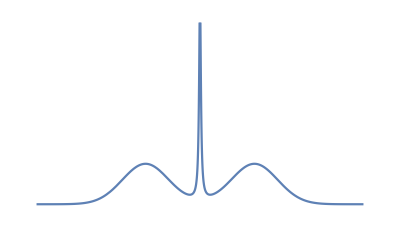

```mathematica
xs = 100;
α=.1;
w=30;
μ=50;
Plot[1/(1+x^2)+0.1+0.2 (Exp[-(x+μ)^2/w^2]+Exp[-(x-μ)^2/w^2]),{x,-150,150},PlotRange->{0,1},Axes->False]
```

## time evolution

simple example with two level system, but the procedure is general and will work for any size hamiltonian

```mathematica
(*build hamiltonian and symbolic ρ*)
Clear[ρ]
Clear[Ω,Δ,Γ];
H = ({{0, 1}, {□, □}});
Ω = 0; Δ =0.1;Γ=0.5;
ρ0={{0.5,0},{0,0.5}};
```

### build master eqs

```mathematica
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t](*[#1,#2][t]*)&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm = rho.H - H.rho ;
linblad =Γ(σm.rho.σp-1/2((σp.σm).rho + rho.(σp.σm)));
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-ⅈ comm[[i,j]]+linblad[[i,j]]];
AppendTo[rhoICPruned,(rho/.t-> 0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]]
]
]
]
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems,i++
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
]
```

```mathematica
rhoPruned
```

{ρ_(1,1)[t],ρ_(1,2)[t],ρ_(2,2)[t]}

```mathematica
eqsPruned
```

{ρ_(1,1)'[t]==0.5 ρ_(2,2)[t],ρ_(1,2)'[t]==(-0.25+0.1 ⅈ) ρ_(1,2)[t],ρ_(2,2)'[t]==(0.+0. ⅈ)-0.5 ρ_(2,2)[t]}

### run

```mathematica
eqsPruned
rhoICPruned
```

{ρ_(1,1)'[t]==0.5 ρ_(2,2)[t],ρ_(1,2)'[t]==(-0.25+0.1 ⅈ) ρ_(1,2)[t],ρ_(2,2)'[t]==(0.+0. ⅈ)-0.5 ρ_(2,2)[t]}

{ρ_(1,1)[0]==0.5,ρ_(1,2)[0]==0,ρ_(2,2)[0]==0.5}

```mathematica
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqsPruned,rhoICPruned], rhoPruned, {t,0,4π}]];
Print["Time to run sim: ",time];
```

Time to run sim: 0.015625

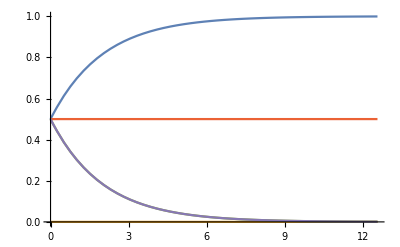

0.5

```mathematica
plt ={};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
AppendTo[plt,{0.5}];(*show 50% population line*)
AppendTo[plt,{ρ0[[1,1]]Exp[-Γ t]}];
Plot[plt, {t, 0, 4π},PlotRange->All]
```

Compare system with no driving field and decay to a system that does not include the ground state, and solves the Schrodinger eq instead

```mathematica
ψ'=ⅈ (0+ⅈ Γ) ψ;(*<-- this will have only one element in ψ, and the solution is Exp[-Γ t] *)
```

```mathematica
13000
```

```mathematica
1.76*^9/13000
```

135385.

```mathematica
2.998/(2 0.85)
```

1.76353